## Adler equation and phase locking (Sec. 11.3.3)

```mathematica
Clear["Global`*"];
```

```mathematica
tend=50;
eq=ψ'[t]== -ν+ Sin[ψ[t]];
init=ψ[0]==0;
sol[ν0_]:=Module[{},
NDSolveValue[{eq,init}/.{ν->ν0},ψ,{t,0,tend}]]
```

```mathematica
ψ1=sol[-1.5];ψ2=sol[-1.1];ψ3=sol[-1.01];ψ4=sol[1.];
```

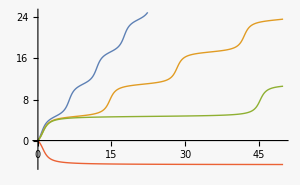

```mathematica
Plot[{ψ1[t],ψ2[t],ψ3[t],ψ4[t]},{t,0,tend},PlotRange->{-5,25},ImageSize->300]
```

```mathematica
gensol=DSolveValue[{eq,init},ψ[t],t]//Simplify
```

2 ArcTan[(1-√(-1+ν^2) Tan[1/2 t √(-1+ν^2)+ArcTan[1/(√(-1+ν^2))]])/ν]